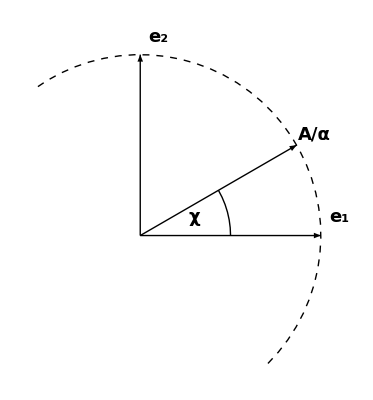

```mathematica
e1=Graphics[{Arrow[{{0,0},{1,0}}]}];
e2=Graphics[{Arrow[{{0,0},{0,1}}]}];
A=Graphics[{Arrow[{{0,0},{(3/4)^(1/2),1/2}}]}];
circ=Graphics[{Dashed,Circle[{0,0},1,{-Pi/4,Pi/2+Pi/5}]}];
circChi=Graphics[{Circle[{0,0},0.5,{0,Pi/6}]}];
(*axesLines=Graphics[{Dashed,Line[{{0,-1.3},{0,1.3}}],Dashed,Line[{{1.3,0},{-1.3,0}}]}];*)
texts=Graphics[{
Text[Style["χ",18,Bold],{0.3,0.1},FormatType->StandardForm],
Text[Style["e_1",18,Bold],{1.1,0.1},FormatType->StandardForm],
Text[Style["e_2",18,Bold],{0.1,1.1},FormatType->StandardForm],
Text[Style["A/α",18,Bold],{(3/4)^(1/2)+0.1,1/2+0.06},FormatType->StandardForm]
}];
Show[e1,e2,A,circ,circChi,texts]
ClearAll[e1,e2,A,circ,circChi,texts]
```